```mathematica
DSolveValue[{y'[x]+y[x]==a Sin[x],y[0]==0},y[x],x]
```

-1/2 a ⅇ^-x (-1+ⅇ^x Cos[x]-ⅇ^x Sin[x])

```mathematica
MatrixExp[({{-x, -i g}, {-i g, -y/2}}) t] // MatrixForm
```

(-(ⅇ^(1/4 t (-2 x-y-√(16 g^2 i^2+4 x^2-4 x y+y^2))) (-2 x+y-√(16 g^2 i^2+4 x^2-4 x y+y^2)))/(2 √(16 g^2 i^2+4 x^2-4 x y+y^2))+(ⅇ^(1/4 t (-2 x-y+√(16 g^2 i^2+4 x^2-4 x y+y^2))) (-2 x+y+√(16 g^2 i^2+4 x^2-4 x y+y^2)))/(2 √(16 g^2 i^2+4 x^2-4 x y+y^2)) | (2 ⅇ^(1/4 t (-2 x-y-√(16 g^2 i^2+4 x^2-4 x y+y^2))) g i)/(√(16 g^2 i^2+4 x^2-4 x y+y^2))-(2 ⅇ^(1/4 t (-2 x-y+√(16 g^2 i^2+4 x^2-4 x y+y^2))) g i)/(√(16 g^2 i^2+4 x^2-4 x y+y^2))
(2 ⅇ^(1/4 t (-2 x-y-√(16 g^2 i^2+4 x^2-4 x y+y^2))) g i)/(√(16 g^2 i^2+4 x^2-4 x y+y^2))-(2 ⅇ^(1/4 t (-2 x-y+√(16 g^2 i^2+4 x^2-4 x y+y^2))) g i)/(√(16 g^2 i^2+4 x^2-4 x y+y^2)) | -(ⅇ^(1/4 t (-2 x-y-√(16 g^2 i^2+4 x^2-4 x y+y^2))) (2 x-y-√(16 g^2 i^2+4 x^2-4 x y+y^2)))/(2 √(16 g^2 i^2+4 x^2-4 x y+y^2))+(ⅇ^(1/4 t (-2 x-y+√(16 g^2 i^2+4 x^2-4 x y+y^2))) (2 x-y+√(16 g^2 i^2+4 x^2-4 x y+y^2)))/(2 √(16 g^2 i^2+4 x^2-4 x y+y^2)))

```mathematica
ExpMatrix[({{-x, -i g}, {-i g, -y/2}}) t] // MatrixForm
```

ExpMatrix[{{-t x,-g i t},{-g i t,-(t y)/2}}]

```mathematica
m={{-x,-i g},{-i g,-y/2}}
```

{{-x,-g i},{-g i,-y/2}}

```mathematica
m//MatrixForm
```

(-x | -g i
-g i | -y/2)

```mathematica
Exp[m t]
```

{{ⅇ^(-t x),ⅇ^(-g i t)},{ⅇ^(-g i t),ⅇ^(-(t y)/2)}}

```mathematica
Exp[m]//MatrixForm
```

(ⅇ^-x | ⅇ^(-g i)
ⅇ^(-g i) | ⅇ^(-y/2))

```mathematica
MatrixExp[m]//MatrixForm
```

(-(ⅇ^(-x/2-y/4-1/4 √(16 g^2 i^2+4 x^2-4 x y+y^2)) (-2 x+y-√(16 g^2 i^2+4 x^2-4 x y+y^2)))/(2 √(16 g^2 i^2+4 x^2-4 x y+y^2))+(ⅇ^(-x/2-y/4+1/4 √(16 g^2 i^2+4 x^2-4 x y+y^2)) (-2 x+y+√(16 g^2 i^2+4 x^2-4 x y+y^2)))/(2 √(16 g^2 i^2+4 x^2-4 x y+y^2)) | (2 ⅇ^(-x/2-y/4-1/4 √(16 g^2 i^2+4 x^2-4 x y+y^2)) g i)/(√(16 g^2 i^2+4 x^2-4 x y+y^2))-(2 ⅇ^(-x/2-y/4+1/4 √(16 g^2 i^2+4 x^2-4 x y+y^2)) g i)/(√(16 g^2 i^2+4 x^2-4 x y+y^2))
(2 ⅇ^(-x/2-y/4-1/4 √(16 g^2 i^2+4 x^2-4 x y+y^2)) g i)/(√(16 g^2 i^2+4 x^2-4 x y+y^2))-(2 ⅇ^(-x/2-y/4+1/4 √(16 g^2 i^2+4 x^2-4 x y+y^2)) g i)/(√(16 g^2 i^2+4 x^2-4 x y+y^2)) | -(ⅇ^(-x/2-y/4-1/4 √(16 g^2 i^2+4 x^2-4 x y+y^2)) (2 x-y-√(16 g^2 i^2+4 x^2-4 x y+y^2)))/(2 √(16 g^2 i^2+4 x^2-4 x y+y^2))+(ⅇ^(-x/2-y/4+1/4 √(16 g^2 i^2+4 x^2-4 x y+y^2)) (2 x-y+√(16 g^2 i^2+4 x^2-4 x y+y^2)))/(2 √(16 g^2 i^2+4 x^2-4 x y+y^2)))

```mathematica
f[x_]:= 1/2 w^2 x^2 +1/2 1/x + l(l+1)/2  1/x^2 
f''(x)
```

x (w^2+(3 l (1+l))/#1^4+1/#1^3&)

```mathematica
f''''(x)
```

x ((60 l (1+l))/#1^6+12/#1^5&)

```mathematica
f'(x)
```

x (-(l (1+l))/#1^3-1/(2 #1^2)+w^2 #1&)

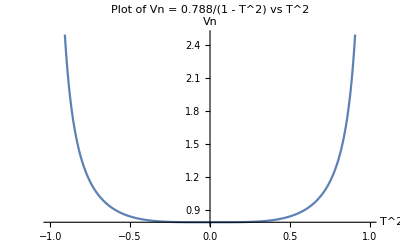

```mathematica
Vn[T_]:=0.788/(1-T^2)

Plot[Vn[T^2],{T,-1,1},AxesLabel->{"T^2","Vn"},PlotLabel->"Plot of Vn = 0.788/(1 - T^2) vs T^2"]
```